## Initialization

```mathematica
$FKKSRoot =  NotebookDirectory[]<>"../";
$SolutionPath = $FKKSRoot<>"Solutions/";
PlotPath = $FKKSRoot<>"Plots/";
LogFile = $FKKSRoot<>"Logs/LogFile.log";
PlotFileExtension = ".png";
NumberofSlaveKernels = Automatic; (*Default should be Automatic*)

(*Import some helper functions*)
Import[FileNameJoin[{$FKKSRoot, "Packages", "HelperFunctions.wl"}]]

(*Setup xAct definitions*)
Import[FileNameJoin[{$FKKSRoot, "Packages", "xActSetup.wl"}]]

(*Setup Proca Solver*)
Import[FileNameJoin[{$FKKSRoot, "Packages", "KerrWithProca.wl"}]]

(*Import mode overtone worker function for iteration routine*)
Import[FileNameJoin[{$FKKSRoot, "Packages", "ModeOvertoneWorker.wl"}]]

(*Setup Energy Momentum Definitions*)
Import[FileNameJoin[{$FKKSRoot, "Packages", "EnergyMomentum.wl"}]]

(*Setup MST Solver*)
Import[FileNameJoin[{$FKKSRoot, "Packages", "MSTSolver.wl"}]]

(*Setup Inhomogeneous Teukolsky Solver*)
Import[FileNameJoin[{$FKKSRoot, "Packages", "TeukolskySolver.wl"}]]
```

```mathematica
ntbdir = "/home/shaunf/Documents/Computer/Code/Project/ProcaAroundKerr/FKKSsolver/KerrDressedWithProca/";
files = FileNames[All, ntbdir<>"Solutions/"];
AllSols = Import/@files;
OrderedSols = Association@@Table["m"<>ToString[m]<>"n"<>ToString[n]->OvertoneModeGroup[n,m,AllSols], {n,0,4},{m,1,4}];
GenerateData[sol_]:={sol["Parameters", "μNv"], sol["Derived", "Einf"]/sol["Derived", "Normalization", "TotalEnergy"]^2}
```

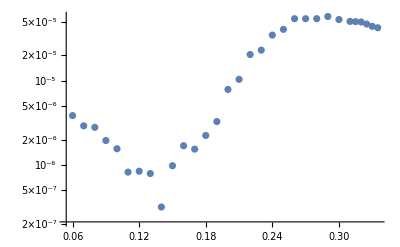

```mathematica
GenerateData/@OrderedSols["m1n0"]//ListLogPlot
```